#### Modified with first and last masses set to 0 position and other masses set to e^(-i^2) and no velocity

```mathematica
m=1.;α=0.25;n=32;tf=1000;p=2;b=0.0;a=1;
```

```mathematica
(*ic=Exp[-i^2];*)
ic = a Sin[π i/(n+1)];

(*ic = a Sin[π i n/(n+1)];*)
```

```mathematica
nsol=NDSolveValue[Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t])(1+ α*(x[i + 1][t] - x[i-1][t]))-b x[i]'[t],{i,n}]/.{x[0][t]:>0,x[n+1][t]:>0},Table[{x[i][0]==ic,x[i]'[0]==0.1},{i,n}]}],Table[x[i],{i,n}],{t,0,tf},MaxSteps->600000,Method->"LSODA"];
```

```mathematica
Table[nsol[[nparticle]][1],{nparticle,1,2}]
```

InterpolatingFunction[{{0., 100.}}, <>][Null]

```mathematica
Plot[Table[nsol[[i]][t], {i, 1,n}], {t, 0, tf}, 
       PlotRange -> All,  Frame -> True, Axes -> False, 
       ImageSize -> 100, AspectRatio -> 1]
```

$Aborted

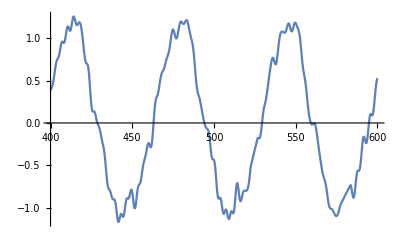

```mathematica
Plot[nsol[[22]][t],{t,400,600}]
```

#### DFT for n = 30 between t = 525 to 600

```mathematica
fpudata=Table[
nsol[[30]][t],{t,525,600,.1}
];
```

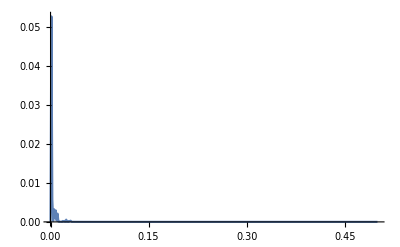

```mathematica
Periodogram[fpudata/maxVal,ScalingFunctions->"Absolute",PlotRange->All]
```

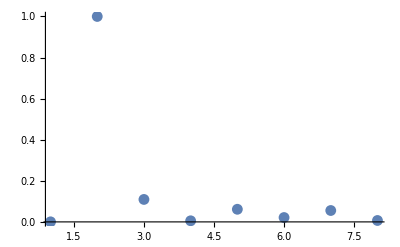

```mathematica
dftFPU=Abs[Fourier[fpudata]]^2/Max[Abs[Fourier[fpudata]]^2];
szFPU=Dimensions[dftFPU][[1]];
dim=Ceiling[0.01szFPU];
dftFPU[[1;;dim]];
(*Periodogram[fpudata,ScalingFunctions->"Absolute",PlotRange->All];*)
ListLinePlot[dftFPU[[1;;dim]],Joined->False,Mesh->All,PlotRange->All]
```

#### Position

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]][tt],{j,1,n}
],Mesh->All,PlotRange->{All,{-2,2}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Position"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->10]//Inactivate;
```

```mathematica
Manipulate[
ListLinePlot[
Table[
nsol[[j]][tt],{j,1,n}
],Mesh->All,PlotRange->{All,{-2,2}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Position"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,10}]//Inactivate;
```

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]][tt]-nsol[[j-1]][tt],{j,2,n}
],Mesh->All,PlotRange->{All,{-1,1}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Position"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->14]//Inactivate;
```

#### Velocity and Momentum calculation

Since NDSolveValue was used, the velocity can be easily calculated using prime notation, viz., velocity = nsol[[j]]’[t]

Here, j is the particle number and t is the current time.

An animation of velocity is below.

```mathematica
Animate[
ListLinePlot[
Table[
nsol[[j]]'[tt],{j,1,n}
],Mesh->All,PlotRange->{All,{-1,1}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Velocity"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->10]//Inactivate;
```

The total Hamiltonian as given in Weissert equation 1.4, page 19

```mathematica
Animate[
ListLinePlot[
Table[
0.5(
(nsol[[j]][tt])^2+(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^2 
)+ (α/3)(nsol[[j]]'[tt]-nsol[[j-1]]'[tt])^3,{j,2,n}
],Mesh->All,PlotRange->{All,{0,1.75}},PlotStyle->{Black,Thin},
Frame->True, FrameLabel->{"Mass", "Velocity"},FrameStyle->Black,BaseStyle->{FontSize->14}
],{tt,0,tf,0.5},AnimationRate->10]//Inactivate;
```

#### Fourier Sine series of solution (position)

#### DFT

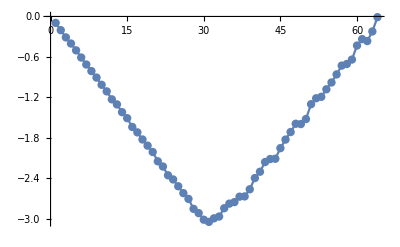

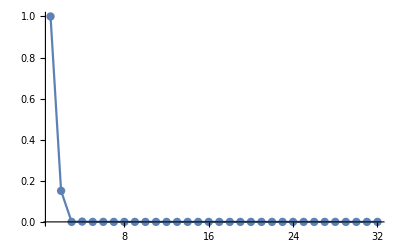

```mathematica
fpudata=Table[
nsol[[jj]][100],{jj,1,n}
];
ListPlot[fpudata,Joined->True,Mesh->All]
dftFPU=Abs[Fourier[fpudata]]^2/Max[Abs[Fourier[fpudata]]^2];
szFPU=Dimensions[dftFPU][[1]];
dim=Ceiling[0.5szFPU];
dftFPU[[1;;dim]];
(*Periodogram[fpudata,ScalingFunctions->"Absolute",PlotRange->All];*)
ListLinePlot[dftFPU[[1;;dim]],Joined->True,Mesh->All,PlotRange->All]
```

#### Comparison with Kuramoto - Sivashinsky

```mathematica
λ=1;a=1.;x0=20.;ν=1/20;tmax=1000.;

sol=NDSolveValue[{D[u[t,x],t]+λ D[u[t,x],x,x,x,x]+ν D[u[t,x],x,x]+u[t,x]D[u[t,x],x]==0,u[0,x]==ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2) ,u[t,-x0]==u[t,x0]},u,{t,0,tmax},{x,-x0,x0},PrecisionGoal->2]
```

InterpolatingFunction[{{0., 1000.}, {…, -20., 20., …}}, <>]

```mathematica
initialCond=Plot[ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2),{x,-20,20},PlotRange->All,PlotStyle->{Thick,Black},BaseStyle->{FontSize->22,Bold},ImageSize->600,Frame->True,FrameLabel->{"X (space)","Amplitude","INITIAL CONDITION"}];
p3d=Plot3D[sol[x,y],{x,0.,tmax},{y,-x0,x0},MaxRecursion->1,Mesh->None,ColorFunction->ColorData["Rainbow"],PlotRange->Full,PlotPoints->100,BaseStyle->{FontSize->8},AxesLabel->{"T","  X","Wave profile,\n u(T,X)"},ImageSize->200,PlotLabel->"Evolution of initial condition \nper the Kuramoto-Sivashinky equation"];
```

```mathematica
Show[p3d]
```

-Graphics3D-

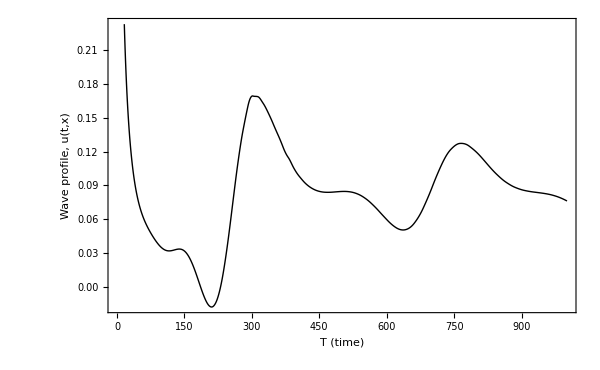

```mathematica
ks1=Table[sol[t,0],{t,0,tmax,tmax/1000}];

ListPlot[ks1,Joined->True,Frame->True,PlotStyle->{Thick,Black},BaseStyle->{FontSize->22,Bold},ImageSize->600,Frame->True,FrameLabel->{"T (time)","Wave profile, u(t,x)"},LabelStyle->Black]
```

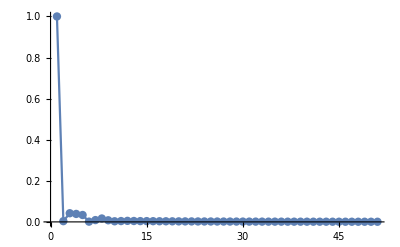

```mathematica
dftKS=Abs[Fourier[ks1]]^2/Max[Abs[Fourier[ks1]]^2];
szKS=Dimensions[dftKS][[1]];
dim=Ceiling[0.05szKS];
dftKS[[1;;dim]];
ListLinePlot[dftKS[[1;;dim]],Joined->True,Mesh->All,PlotRange->All]
```